```mathematica
(*Note: remember the FullSimplify --> Expand vs. Expand --> FullSimplify*)
(*Aftering adding pressure inertia , pressure force, gravitating role of prssure. to fluid equations, do I also change...*)
(*Things to check: including the third term, Subscript[ρ, 0], H(a), Ψ(a), Subscript[Ω, r]*)
(*Analytic solution to the radiation-dominated perturbation equation, and a variable transform from time domain to scale space*)
ClearAll["Global`*"]
n=-1/2;δ=f[x]*x^n;  δDot=D[δ,x]*k ;δDotDot=D[δDot,x]*k; (*Adjust n, to once again cancel first-order damping term*)
perturbationEqn=δDotDot+1/t δDot==1/t^2(1 -(3 cs^2 k^2)/(32π G Subscript[ρ, 0] a^2))δ/.t->x/k/.Subscript[ρ, 0]->(3 H0^2)/(8 π G a^3); (*Radiation dominated perturbation equation -> vary form for cool stuff*)
FofX=DSolve[perturbationEqn,f[x],x][[1,1,2]];
δofX=FofX*x^n//FullSimplify//Expand;(*MUST be in this exact order*)
δofKA=δofX/.x->((2k a^(3/2))/(3 H0))
```

(3/2)^((√(-3 H0^2+a cs^2 k^2) √(-1+H0^2/(-3 H0^2+a cs^2 k^2)))/(2 H0)) ((a^(3/2) k)/H0)^(-(√(-3 H0^2+a cs^2 k^2) √(-1+H0^2/(-3 H0^2+a cs^2 k^2)))/(2 H0)) C[1]+(2/3)^((√(-3 H0^2+a cs^2 k^2) √(-1+H0^2/(-3 H0^2+a cs^2 k^2)))/(2 H0)) ((a^(3/2) k)/H0)^((√(-3 H0^2+a cs^2 k^2) √(-1+H0^2/(-3 H0^2+a cs^2 k^2)))/(2 H0)) C[2]

```mathematica
H[a_]:=H0 √(Ωr/a^4); (*Adjusting cosmological parameters, a^-4 and Subscript[Ω, m] -> Subscript[Ω, r]*)
Ψ[a_]:=-(3 H0^2 Ωr)/(2 a^3);
(*Solving perturbation equation for negligible and non-negligible sound speed cases*)(*CHANGE THESE EQUATIONS*)
ceff2[a_]:=0;
negligibleSolution=DSolve[a^2 H[a]^2 Δa''[a]+(3 a H[a]^2+a^2 H[a] H'[a]) Δa'[a]+(k^2 ceff2[a]^2/a^2+Ψ[a]) Δa[a]==0,Δa,a]//FullSimplify;
ceff2[a_]:=cs^2;
perturbedSolution=DSolve[a^2 H[a]^2 Δa''[a]+(3 a H[a]^2+a^2 H[a] H'[a]) Δa'[a]+(k^2 ceff2[a]^2/a^2+Ψ[a]) Δa[a]==0,Δa,a]//FullSimplify;
negligibleFunc=negligibleSolution[[1,1,2]];
perturbedFunc=Function[{a},(3/2)^((√(-3 H0^2+a cs^2 k^2) √(-1+H0^2/(-3 H0^2+a cs^2 k^2)))/(2 H0)) ((a^(3/2) k)/H0)^(-(√(-3 H0^2+a cs^2 k^2) √(-1+H0^2/(-3 H0^2+a cs^2 k^2)))/(2 H0)) C[1]+(2/3)^((√(-3 H0^2+a cs^2 k^2) √(-1+H0^2/(-3 H0^2+a cs^2 k^2)))/(2 H0)) ((a^(3/2) k)/H0)^((√(-3 H0^2+a cs^2 k^2) √(-1+H0^2/(-3 H0^2+a cs^2 k^2)))/(2 H0)) C[2]];
(*Matching functions and derivatives at the start and end of the "kick"*)
solutionsForConstants1=Solve[{ai CC==perturbedFunc[ai],CC==D[perturbedFunc[a],a]/. a->ai},{C[1],C[2]}]//FullSimplify;
startKick =perturbedFunc /. {C[1]->solutionsForConstants1[[1,1,2]], C[2]->solutionsForConstants1[[1,2,2]]};
solutionsForConstants2=Solve[{(negligibleFunc[af])==(startKick[af]),(D[negligibleFunc[a],a]/. a->af)==(D[startKick[a],a]/. a->af)},{C[1],C[2]}]//Simplify;
endKick = negligibleFunc /. {C[1]->solutionsForConstants2[[1,1,2]], C[2]->solutionsForConstants2[[1,2,2]]};
Print["Completed."]
```

Completed.

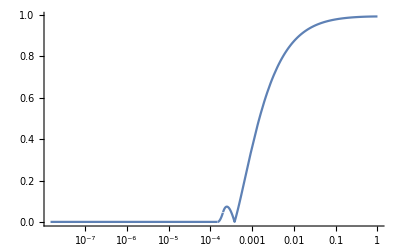

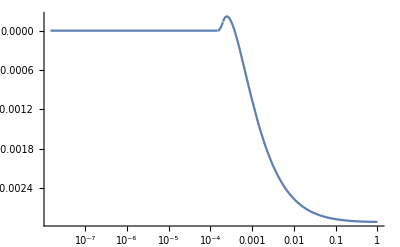

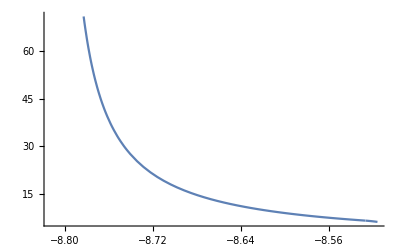

```mathematica
(*Plotting*)
Clear[h,H0,Ωr,k,ai,af]
h=0.7; H0=0.0003335 h; Ωr=1; k=0.00528; ai=0.0001489; af=0.00020; da = Log[af/ai]; cs2want=0.0001;cs=√(cs2want/da);CC=1; (*fix Ωr..*)
f[a_]:=-(CC a-δgdm[a])/(CC a );g[a_]:=-f[a];lg[a_]:=Log[g[a]];
δgdm[a_]:=Piecewise[{{CC a,a<ai},{startKick[a],ai≤ a≤ af}},endKick[a]];

LogLinearPlot[{(Abs[CC a-δgdm[a]])/(CC a )},{a,0.0001*ai,1},PlotRange->All](*Note: absolute value*)
LogLinearPlot[(-δgdm[a]*Ψ[a]*a^2+CC*a*Ψ[a]*a^2)/k^2,{a,0.0001* ai,1}]
Plot[(lg[Exp[x+0.01]]-lg[Exp[x-.01]])/0.02,{x,Log[ai]-0.001,Log[af]+0.001}]
```